```mathematica
Needs["Histograms`"]
```

```mathematica
x0=0.53;
sigma0=0.04;
x1=1.18;
sigma1=0.24;
bins = Table[i,{i,0,2.4,0.04}];
t1=RandomReal[NormalDistribution[x0,sigma0],100];
t2=RandomReal[NormalDistribution[x1,sigma1],200];
t3=Join[t1,t2];
p1=Histogram[t3,Frame->True,FrameTicksStyle-> Thick, FrameLabel->{"Fall Times (s)","Counts"},HistogramRange->{0,2.0},HistogramCategories->bins,
PlotRangePadding->0,
LabelStyle->FontSize->18,
AspectRatio->1/1.5,
TicksStyle -> Blue,
ImageSize->6.5*72];
Mean[t3]
StandardDeviation[t3]
```

0.938361

0.357747

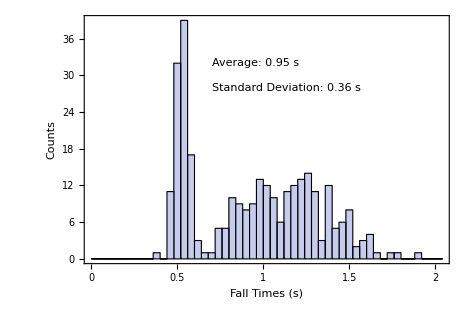

```mathematica
p2 = Show[p1,
Graphics[Text[" ",{1.0,39.0},{-1,0},TextStyle->FontSize->16] ],
Graphics[Text["Average: 0.95 s",{0.7,32.0},{-1,0},TextStyle->FontSize->20] ],
Graphics[Text["Standard Deviation: 0.36 s",{0.7,28.0},{-1,0},TextStyle->FontSize->20] ]
]
```

```mathematica
"/media/flash/131f08/labs/f08/SampleHist1.eps"
```

/media/flash/131f08/labs/f08/SampleHist1.eps